# Script for Eccentric Inspiral used as initial data for Merger, q =1

## Initial Parameters and calculating (x,e_t)

```mathematica
ClearAll["Global'*"]; Off[General::spell];
SetOptions[Simplify,TimeConstraint->1000];
Clear[m1,m2,M,μ,η,c, G, M0, T, L, AU, fGWLow,ωorbLow,xLow,a0, a0L, etLow,xdot0PN ,xdot1PN ,xdot2PN ,xdot3PN ,etdot0PN,etdot1PN,etdot2PN,etdot3PN,xdot,etdot,solxet3PN,x,et,n1PN,n2PN,n3PN,ldot,soll3PN,l,βt,αADM3PN,AsADM,u3PNADM,dt,u3PNADMtable,u3PNADMvstime,u3PNADMvstime1,u3PNADMinterp,tArray,r0PN,r1PN,r2PN,r3PN,r,phid0PN,phid1PN,phid2PN,phid3PN,phidot,rinterp,rvstime,rvstime1,rtab,phi,solphi3PN,hre]
$MinPrecision=20; (* $MachinePrecision;*)
```

### We consider a normalized equal mass binary where time is in units of solar masses.

Mass in units of solar mass

```mathematica
m1 =0.5000000618087954;
m2=1-m1;
M=m1+m2;
μ=(m1*m2)/M;
```

```mathematica
γ=0.5772156649
```

0.577216

Symmetric Mass Ratio

```mathematica
η=N[μ/M]
```

0.25

Value for eccentricity

```mathematica
e0 = 10^-3
```

1/1000

## Calculation of the evolution time

```mathematica
c=299792458; G=6.67428 10^-11;  M0=1.98892 10^30;
T = M0 G c^-3 ; L=M0 G c^-2; AU = 1.496 10^12;
```

```mathematica
fGWLow = N[1000*T];
ωorbLow=fGWLow *π
Plow = (2 π)/ωorbLow T
xLow=(M*ωorbLow)^(2/3)
rLow= N[M/xLow]
```

0.0154778

0.002

0.0621069

16.1013

```mathematica
Ma0=(ωorbLow)^(-2/3);
a0 =M^(1/3)/(ωorbLow)^(2/3)
a0 L (*in meters*)
Tc =Simplify[ 5/256 a0^4/(m1 m2 M)]
Tcs = Tc T (*in seconds*)
```

16.1013

23781.6

5250.87

0.0258697

```mathematica
c0 = (8.701265789680349 a0 (1.-e0^2))/((304.+121. e0^2)^(870/2299))
Te =Simplify[ 5/256 c0^4/(m1 m2 M)]
Tes = Te T (*in seconds*)
```

16.1013

5250.85

0.0258696

time at Light Ring, which is ISCO for equal mass  (20 M)

```mathematica
TcIS =Simplify[ 5/256(4 M)^4/(m1 m2 M)]
```

20.

However, if we consider that the final black hole will spin, rISCO<4

```mathematica
rLR = 4 ;
MωLR =(rLR)^(-3/2);
```

```mathematica
xLR = N[(rLR MωLR)^2 ]
Sqrt[xLR]  (*speed at light ring*)
```

0.25

0.5

### Now that initial values are determined, we begin coding the PN corrections for x and e_t up to the 3rd order (+3.5 HT).

We choose a moderate initial eccentricity. (want to find the largest we can make this while still reaching the quasi-circular limit) et<0.001

```mathematica
etLow=e0
```

1/1000

Those are the instantaneous terms for xdot taken from arXiv:1609.05933 (A3-A6)

```mathematica
xdot0PN = (2(37 et[t]^4+292 et[t]^2+96)η)/(15(1-et[t]^2)^(7/2));
xdot1PN= η/(420(1-et[t]^2)^(9/2))(-(8288η-11717)et[t]^6-14(10122η-12217)et[t]^4-120(1330η-731)et[t]^2-16(924η+743));
xdot2PN = η/(45360(1-et[t]^2)^(11/2))((1964256 η^2-3259980η+3523113)et[t]^8+(64828848 η^2-123108426η+83424402)et[t]^6+(16650606060 η^2-207204264η+783768)et[t]^4+(61282032 η^2+15464736η-92846560)et[t]^2+1903104 η^2+(1-et[t]^2)^(1/2)((2646000-1058400η)et[t]^6+(64532160-25812864η)et[t]^2-580608η+1451520)+4514976η-360224);
xdot3PN=η/(598752000(1-et[t]^2)^(13/2))(25 et[t]^10(2699947161-176η(4η(2320640η-2962791)+16870887))+32 et[t]^2(55η(270(7015568(1-et[t]^2)^(1/2)-9657701)η-8125851600(1-et[t]^2)^(1/2)+38745 π^2(1121(1-et[t]^2)^(1/2)+1185)-901169500 η^2+5387647438)+31050413856(1-et[t]^2)^(1/2)+358275866598)+128(-275η(81(16073-17696(1-et[t]^2)^(1/2))η-1066392(1-et[t]^2)^(1/2)+46494 π^2((1-et[t]^2)^(1/2)-45)+470820 η^2+57265081)-3950984268(1-et[t]^2)^(1/2)+12902173599)+et[t]^8(162(1240866000(1-et[t]^2)^(1/2)+19698134267)-1100η(16η(-3582684(1-et[t]^2)^(1/2)+137570300η-286933509)+27(6843728(1-et[t]^2)^(1/2)+255717 π^2+173696120)))+12 et[t]^6(55η(90(52007648(1-et[t]^2)^(1/2)+311841025)η+3(4305 π^2(14(1-et[t]^2)^(1/2)-19113)-5464335200(1-et[t]^2)^(1/2)+767166806)-17925404000 η^2)+742016570592(1-et[t]^2)^(1/2)+6005081022)+8 et[t]^4(55η(270(71069152(1-et[t]^2)^(1/2)+6532945)η-74508169680(1-et[t]^2)^(1/2)+116235 π^2(1510(1-et[t]^2)^(1/2)-4807)-23638717900 η^2+88628306866)+6(332891836596(1-et[t]^2)^(1/2)+8654689873))+40677120(891 et[t]^8+28016 et[t]^6+82736 et[t]^4+43520 et[t]^2+3072)Log[x[t]/xLow*(1+(1-et[t]^2)^(1/2))/(2(1-et[t]^2))]);
```

Those are the instantaneous terms for etdot taken from arXiv:0908.3854v2 (6.19a-6.19d)

```mathematica
etdot0PN=(-et[t](121 et[t]^2+304)η)/(15(1-et[t]^2)^(5/2));
etdot1PN = (et[t]*η)/(2520(1-et[t]^2)^(7/2))((93184η-125361)et[t]^4+12(54271η-59834)et[t]^2+8(28588η+8451));
etdot2PN = (-et[t]*η)/(30240(1-et[t]^2)^(9/2))((2758560 η^2-4344852η+3786543)et[t]^6+(42810096 η^2-78112266η+46579718)et[t]^4+(48711348 η^2-35583228η-36993396)et[t]^2+4548096 η^2+(1-et[t]^2)^(1/2)((2847600-1139040η)et[t]^4+(35093520-14037408η)et[t]^2-5386752η+13466880)+13509360η-15198032);
etdot3PN=(-et[t]η)/((1-et[t]^2)^(11/2))(54177075619/6237000+(7198067/22680+1283/10 π^2)η-3000281/2520 η^2-61001/486 η^3+et[t]^2(6346360709/891000+(9569213/360+54001/960 π^2)η+12478601/15120 η^2-86910509/19440 η^3)+et[t]^4(-126288160777/16632000+(418129451/181440-254903/1920 π^2)η+478808759/20160 η^2-2223241/180 η^3)+et[t]^6(5845342193/1232000+(-98425673/10080-6519/640 π^2)η+6538757/630 η^2-11792069/2430 η^3)+et[t]^8(302322169/1774080-1921387/10080 η+41179/216 η^2-193396/1215 η^3)+(1-et[t]^2)^(1/2)(-22713049/15750+(-5526991/945+8323/180 π^2)η+54332/45 η^2+et[t]^2(89395687/7875+(-38295557/1260+94177/960 π^2)η+681989/90 η^2)+et[t]^4(5321445613/378000+(-26478311/1512+2501/2880 π^2)η+225106/45 η^2)+et[t]^6(186961/336-289691/504 η+3197/18 η^2))+730168/23625*1/(1+(1-et[t]^2)^(1/2))+304/15(82283/1995+297674/1995 et[t]^2+1147147/15960 et[t]^4+61311/21280 et[t]^6)Log[x[t]/xLow*(1+(1-et[t]^2)^(1/2))/(2(1-et[t]^2))]);
```

## Now we begin coding the High Accuracy terms

The more accurate calculation of the functions entering in the hereditary terms up to eccentricity 0.7 are: arXiv:1609.05933 ϕe (A11), tϕe (A12), φe(A10)

```mathematica
ε=(1.-et[t]^2)^(-1/2);
aϕe = ε^10(1.+18970894028/2649026657 et[t]^2+157473274/30734301 et[t]^4+48176523/177473701 et[t]^6+9293260/3542508891 et[t]^8-5034498/7491716851 et[t]^10+ 428340/9958749469 et[t]^12);
atϕe = ε^7(1.+413137256/136292703 et[t]^2+37570495/98143337 et[t]^4-2640201/993226448 et[t]^6-4679700/6316712563 et[t]^8-328675/8674876481 et[t]^10);
aφee=192/985((1-et[t]^2)^(1/2))/et[t]^2((1-et[t]^2)^(1/2)aϕe -atϕe);
```

More functions entering in the hereditary terms: arXiv:1609.05933 ψe(A13), ζe(A14), κe(A15)

```mathematica
aψe=ε^12(1.- 185/21 et[t]^2-3733/99 et[t]^4-1423/104 et[t]^6);
aζe=ε^12(1.+ 2095/143 et[t]^2+1590/59 et[t]^4+977/113 et[t]^6);
aκe=ε^14(1.+ 1497/79 et[t]^2+7021/143 et[t]^4+997/98 et[t]^6+463/51 et[t]^8-3829/120 et[t]^10);
```

And their tilde: arXiv:1609.05933 tψe(A16), tζe(A17), tκe(A18)

```mathematica
atψe=ε^9(1- 2022/305 et[t]^2-249/26 et[t]^4-193/239 et[t]^6+23/43 et[t]^8-102/463 et[t]^10);
atζe=ε^9(1+ 1563/194 et[t]^2+1142/193 et[t]^4+123/281 et[t]^6-27/328 et[t]^8);
atκe=ε^10(1+ 1789/167 et[t]^2+5391/340 et[t]^4+2150/219 et[t]^6-1007/320 et[t]^8+2588/189 et[t]^10);
```

And now, from arXiv:0908.3854, we take Fe (6.9),  ψne(6.22a), ζne(6.22b)

```mathematica
aFe=ε^13(1+85/6 et[t]^2+5171/192 et[t]^4+1751/192 et[t]^6+297/1024 et[t]^8);
aψne=1344/17599 (7-5 et[t]^2)/(1-et[t]^2) aϕe  + 8191/17599 aψe;
aζne=583/567 aζe-16/567 aϕe ;
```

And last, from arXiv:0908.3854, follows φee is the same (see 6.22h), ψee(6.22i), ζee(6.22j), kee(6.22k) and lastly Fee(6.23)

```mathematica
aψee=18816/55691 1/(et[t]^2(1-et[t]^2)^(1/2)) ((1-et[t]^2)^(1/2)(1-11/7 et[t]^2)aϕe -(1-3/7 et[t]^2)atϕe )+16382/55691 ((1-et[t]^2)^(1/2))/et[t]^2((1-et[t]^2)^(1/2)aψe-atψe);
aζee=924/19067 1/(et[t]^2(1-et[t]^2)^(1/2)) (-(1-et[t]^2)^(3/2)aϕe +(1-5/11 et[t]^2)atϕe)+12243/76268 ((1-et[t]^2)^(1/2))/et[t]^2((1-et[t]^2)^(1/2)aζe-atζe);
aκee=((1-et[t]^2)^(1/2))/et[t]^2((1-et[t]^2)^(1/2)aκe-atκe)(769/96-3059665/700566 Log[2.] +8190315/1868176 Log[3.])^-1;
aFee=ε^11(1+2782/769 et[t]^2+10721/6152 et[t]^4+1719/24608 et[t]^6);
```

## Using High accuracy Hereditary Terms “a”

Those are the hereditary terms for xdot taken from arXiv:1609.05933 (A7)

```mathematica
xdotHT = η x[t]^(13/2)((256 π)/5 aϕe+((256 π)/(1-et[t]^2)aϕe+2/3(-(17599 π)/35 aψne -(2268 η π)/5 aζne -(788 π et[t]^2)/(1-et[t]^2)aφee))x[t] +64/18375(-116761 aκe +(19600 π^2 - 59920 γ-59920 Log[(4 x[t]^(3/2))/xLow])aFe)x[t]^(3/2));
```

Those are the hereditary terms for etdot  taken from arXiv:1609.05933 (A20)

```mathematica
etdotHT =  32/5 et[t]η x[t]^4(-985/48 π x[t]^(3/2)aφee+π x[t]^(5/2) (55691/1344 aψee + 19067/126 η aζee) + x[t]^3((89789209/352800-87419/630 Log[2.]+78003/560 Log[3.]) aκee -769/96(16/3 π^2 -1712/105 γ-1712/105 Log[(4 x[t]^(3/2))/xLow] )aFee));
```

## Adding the 6PN Quasi-circular corrections

```mathematica
xdot3p5PNQC=(64π)/5*η*x[t]^5*(-4415/4032+358675/6048 η+91945/1512 η^2)x[t]^(7/2);
α0=153.8803;
α1=-55.13;
α2=588;
α3=-1144;
a4=-5η*α0-(97 η^4)/3888-(18929389 η^3)/435456-(3157 π^2*η^2)/144+(54732199 η^2)/93312-47468/315*η*Log[x[t]]-(31495 π^2*η)/8064-(856γ*η)/315+(59292668653η)/838252800-1712/315 η*Log[2]+(124741Log[x[t]])/8820-(361 π^2)/126+(124741γ)/4410+3959271176713/25427001600-(47385Log[3])/1568+(127751Log[2])/1470;
a4p5=(9731π*η^3)/1344+(42680611π*η^2)/145152+(205 π^3 η)/6-(51438847π*η)/48384-3424/105 π*Log[x[t]]-(6848γ*π)/105+(343801320119π)/745113600-13696/105 π*Log[2];
a5=(155α0*η^2)/12+(1195α0*η)/336-6η*α1-(11567 η^5)/62208+(51474823 η^4)/1741824+(9799 π^2*η^3)/384-(9007776763 η^3)/11757312+216619/189 η^2*Log[x[t]]-(126809 π^2*η^2)/3024-(2354γ*η^2)/945+(1362630004933 η^2)/914457600-4708/945 η^2*Log[2]+(53963197η*Log[x[t]])/52920+(14555455 π^2*η)/217728+(3090781γ*η)/26460-(847101477593593η)/228843014400-(15795η*Log[3])/3136+(2105111η*Log[2])/8820-(5910592*Log[x[t]])/1964655-(21512 π^2)/1701-(11821184γ)/1964655+29619150939541789/36248733480960+(616005Log[3])/3136-(107638990Log[2])/392931;
a5p5=-20*π*η*α0+(49187π*η^4)/6048-(7030123π*η^3)/13608-(112955 π^3*η^2)/576+(1760705531π*η^2)/290304-189872/315 π*η*Log[x[t]]-(26035 π^3*η)/16128-(3424γ*π*η)/315-(2437749208561π*η)/4470681600-6848/315 π*η*Log[2]+(311233π*Log[x[t]])/11760+(311233γ*π)/5880+(91347297344213π)/81366405120-142155/784 π*Log[3]+(5069891π*Log[2])/17640;
a6=-(535α0*η^3)/36+(7295α0*η^2)/336-(248065α0*η)/4536+(31α1*η^2)/2+(239α1*η)/56-7α2*η-7α3*η*Log[x[t]]-α3*η-(155377 η^6)/1679616-(152154269 η^5)/10450944-(1039145 π^2*η^4)/62208+(76527233921 η^4)/94058496-(41026693 η^3*Log[x[t]])/17010+(55082725 π^2*η^3)/217728-(2033γ*η^3)/1701-(56909847373567 η^3)/7242504192-(4066 η^3*Log[2])/1701-(271237829 η^2*Log[x[t]])/127008+(92455 π^4*η^2)/1152-(4061971769 π^2*η^2)/870912-(21169753γ*η^2)/317520+(3840832667727673 η^2)/55477094400-(57915 η^2*Log[3])/12544-(2724535 η^2*Log[2])/21168-4387/63 π^2*η*Log[x[t]]-(12030840839η*Log[x[t]])/37721376+(410 π^4*η)/9-8774/63 γ*π^2*η+(206470485307 π^2*η)/1005903360+(362623282541γ*η)/94303440-(12413297162366594971η)/271865501107200+(3016845η*Log[3])/12544-17548/63 π^2*η*Log[2]+(701463800861η*Log[2])/94303440+(366368 Log[x[t]]^2)/11025+(2930944Log[2]Log[x[t]])/11025-13696/315 π^2*Log[x[t]]+(1465472γ*Log[x[t]])/11025-(155359670313691Log[x[t]])/157329572400-(27392*N[Zeta[3],25])/105-(256 π^4)/45-(27392γ*π^2)/315+(1414520047 π^2)/2619540+(1465472 γ^2)/11025-(155359670313691γ)/78664786200+1867705968412371074441833/154211174411374080000+(5861888 Log[2]^2)/11025-(37744140625Log[5])/260941824-(63722699919Log[3])/112752640-54784/315 π^2*Log[2]+(5861888γ*Log[2])/11025-(206962178724547Log[2])/78664786200;
xdot4to6PNQC=(64η*x[t]^5)/5(a4*x[t]^4+a4p5*x[t]^(9/2)+a5*x[t]^5+a5p5*x[t]^(11/2)+a6*x[t]^6);
```

## Now for the High Accuracy Hereditary Corrections and Instantaneous terms

```mathematica
xdotINSTHT=1/M(xdot0PN*x[t]^5+xdot1PN*x[t]^6+xdot2PN*x[t]^7+xdot3PN*x[t]^8+xdotHT+xdot3p5PNQC
+xdot4to6PNQC);
etdotINSTHT = 1/M(etdot0PN*x[t]^4+etdot1PN*x[t]^5+etdot2PN*x[t]^6+etdot3PN*x[t]^7+etdotHT);
```

```mathematica
solxet3PNINSTHT=NDSolve[{x'[t]==xdotINSTHT,et'[t]==etdotINSTHT,x[0]==xLow,et[0]==etLow},{x[t],et[t]},{t,0,Infinity}, Method->{"StiffnessSwitching"},AccuracyGoal->Automatic, WorkingPrecision->$MinPrecision, PrecisionGoal->$MinPrecision];
```

NDSolve::precw: The precision of the differential equation ({«1»}) is less than WorkingPrecision (20.).

NDSolve::ndsz: At t == 4712.9480731208607008, step size is effectively zero; singularity or stiff system suspected.

```mathematica
(*xdotINSTHTnoe=xdotINSTHT/.et[t]->0*)
```

Will need to replace tStiff for different parameters

```mathematica
tStiff=4712.94807312079510734711570984589816849854`20;
tfinins=tStiff;
Simplify[ tfinins - Te]
```

-537.899

```mathematica
x3PN[t_]:=Evaluate[x[t]/.solxet3PNINSTHT]
```

```mathematica
et3PN[t_]:=Evaluate[et[t]/.solxet3PNINSTHT]
```

we define  tISCO = tStiff - 20M, for a0 = 4M, from where the eq. becomes stiff.

```mathematica
tISCO =tfinins-TcIS
```

4692.95

```mathematica
tISCO*T
```

0.0231209

```mathematica
ScientificForm[x3PN[tISCO]]
```

{1.78329×10^-1}

```mathematica
ScientificForm[et3PN[tISCO]]
```

{1.30469×10^-4}

```mathematica
Solve[0.17329==(MωISCO)^(2/3),MωISCO]
```

{{MωISCO→0.0721374}}

### I tabulate the time values to convert to time in seconds. This allows me to create x,et plots with time in seconds.

```mathematica
dt=TcIS/20
```

1.

```mathematica
ScientificForm[dt T]
```

4.92674×10^-6

```mathematica
Ntab = IntegerPart[tfinins/dt]
```

4712

```mathematica
tfintab = Ntab dt
```

4712.

```mathematica
ScientificForm[tfintab T]
```

2.32148×10^-2

```mathematica
tinit = tfinins - tfintab
```

0.948073

```mathematica
tArrayINSTHTSM=Table[t,{t,0,tfintab,dt}];
tArrayINSTHTSec=Table[t*(4.93*10^-6),{t,0,tfintab,dt}];
x3PNINSTHTArray=Table[x3PN[t],{t,0,tfintab,dt}];
x3PNINSTHTvstimeSM=Partition[Riffle[tArrayINSTHTSM,x3PNINSTHTArray],2];
x3PNINSTHTvstimeSec=Partition[Riffle[tArrayINSTHTSec,x3PNINSTHTArray],2];
x3PNINSTHTvstimeSec1=MapAt[Delete[#,0]&,x3PNINSTHTvstimeSec,{All,2}];
x3PNINSTHTvstimeSM1=MapAt[Delete[#,0]&,x3PNINSTHTvstimeSM,{All,2}];
```

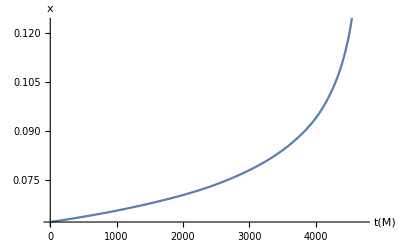

```mathematica
Show[Plot[x3PN[t],{t,0,tfintab},AxesLabel->{Style["t(M)",Bold,16],Style["x",Bold,16]},PlotStyle->{Thickness[0.002],Black}],ListLinePlot[x3PNINSTHTvstimeSM1]]
```

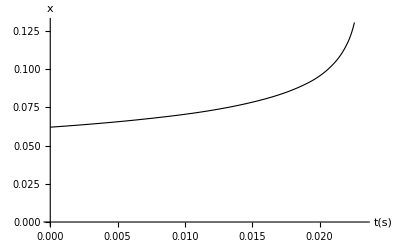

```mathematica
ListLinePlot[x3PNINSTHTvstimeSec1,AxesLabel->{Style["t(s)",Bold,16],Style["x",Bold,16]},PlotStyle->{Thickness[0.002],Black}]
```

```mathematica
et3PNINSTHTArray=Table[et3PN[t],{t,0,tfintab,dt}];
et3PNINSTHTvstimeSec=Partition[Riffle[tArrayINSTHTSec,et3PNINSTHTArray],2];
et3PNINSTHTvstimeSec1=MapAt[Delete[#,0]&,et3PNINSTHTvstimeSec,{All,2}];
```

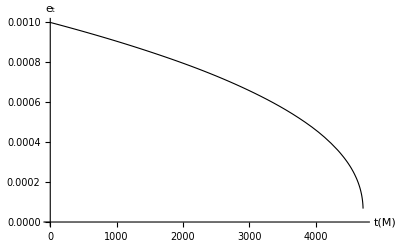

```mathematica
Plot[et3PN[t],{t,0,tfintab},AxesLabel->{Style["t(M)",Bold,16],Style["e_t",Bold,16]},PlotStyle->{Thickness[0.002],Black}]
```

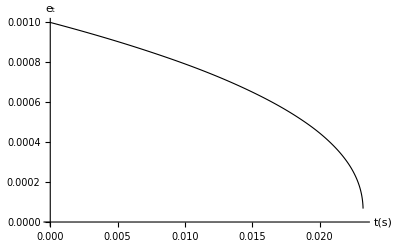

```mathematica
ListLinePlot[et3PNINSTHTvstimeSec1,AxesLabel->{Style["t(s)",Bold,16],Style["e_t",Bold,16]},PlotStyle->{Thickness[0.002],Black}]
```

## We now work towards finding the eccentric anomaly u.

### We need to find the mean anomaly l since we use it to determine the eccentric anomaly. (See section 2.1)

We use the relation between the mean motion n and the mean anomaly from Eq (3.9) to find l(t).
The PN corrections for the mean motion are as follows.

```mathematica
n1PN = 3/(et3PN[t]^2-1);
n2PN = ((26η-51)et3PN[t]^2+28η-18)/(4(et3PN[t]^2-1)^2);
n3PN = -1/(128(1-et3PN[t]^2)^(7/2))((1536η-3840)et3PN[t]^4+(1920-768η)et3PN[t]^2-768η+(1-et3PN[t]^2)^(1/2)((1040 η^2-1760η+2496)et3PN[t]^4+(5120 η^2+123 π^2 η-17856η+8544)et3PN[t]^2+896 η^2-14624η+492 η π^2-192)+1920);
```

We solve the differential and obtain the equation for the mean anomaly.

```mathematica
ldot = 1/M(x3PN[t]^(3/2)+n1PN*x3PN[t]^(5/2)+n2PN*x3PN[t]^(7/2)+n3PN*x3PN[t]^(9/2));
```

```mathematica
soll3PN=NDSolve[{l3PN'[t]- ldot ==0,l3PN[0]==π},l3PN[t],{t,0,tfinins}, Method->{"StiffnessSwitching"},AccuracyGoal->Automatic, WorkingPrecision->$MinPrecision, PrecisionGoal->$MinPrecision];
```

NDSolve::precw: The precision of the differential equation ({{{-1. (Power[«2»]+Times[«3»]+Times[«4»]+Times[«4»])+l3PN'[t]}==0,l3PN[0]==π},{},{},{},{}}) is less than WorkingPrecision (20.).

```mathematica
l[t_]:=Evaluate[l3PN[t]/.soll3PN]
```

### We now use ADM coordinates to code the terms contained in the equation for eccentric anomaly seen in Eq(3.4).

```mathematica
βt[t_]:=(1-(1-et3PN[t]^2)^(1/2))/et3PN[t];
αADM3PN[t_]:=βt[t]^j(x3PN[t]^2((15-6η)/(j(1-et3PN[t]^2)^(1/2))-(4η+η^2)/4)+x3PN[t]^3((2880(1+et3PN[t]^2)-(10880+2784 et3PN[t]^2-123 π^2)η+(960+1056 et3PN[t]^2)η^2)/(96j(1-et3PN[t]^2)^(3/2))+(7488-(7544-48 et3PN[t]^2-3 π^2)η+(1168+32 et3PN[t]^2)η^2-52(1-et3PN[t]^2)η^3)/(96(1-et3PN[t]^2))+j*(-18η+24 η^2+3 η^3)/(16(1-et3PN[t]^2)^(1/2))+j^2*(13 η^3)/48));
```

The term below comes from equation (3.5) of my thesis and contains the Bessel functions that are used for the eccentric anomaly. Three Bessel functions are used, two of which are contained in a double sum. Bessel functions are quickly programmed and evaluated in Mathematica with a simple command. For example, the command “BesselJ[n,x]” sums over the first argument (n) and is a function of the second argument (x).

```mathematica
AsADM[t_]:= 2/s BesselJ[s,s*et3PN[t]]+Sum[αADM3PN[t](BesselJ[j+s,s*et3PN[t]]-BesselJ[s-j,s*et3PN[t]]),{j,1,10}];
```

We truncate the sums at 10 and obtain the eccentric anomaly. We chose this truncation value because it allowed for evaluation of the Bessel functions in a reasonable amount of time without loss of accuracy.

```mathematica
u3PNADM[t_]:= l[t]+Sum[AsADM[t]*Sin[s*l[t]],{s,1,10}];
```

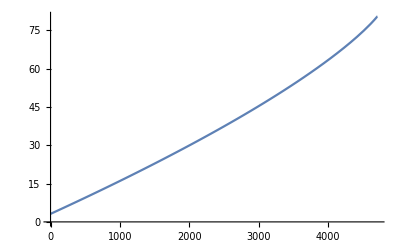

```mathematica
Plot[u3PNADM[t],{t,0,tfinins}]
```

### To interpolate this function, we need to tabulate its values.

We combine the tabulated values of the eccentric anomaly and the time array to create an interpolating function.

```mathematica
tArray=Table[t,{t,0,tfintab,dt}];
```

```mathematica
Timing[u3PNADMtable=Table[u3PNADM[t],{t,0,tfintab,dt}] ;]
```

{73.1113,Null}

```mathematica
u3PNADMvstime=Partition[Riffle[tArray,u3PNADMtable],2];
```

```mathematica
u3PNADMvstime1=MapAt[Delete[#,0]&,u3PNADMvstime,{All,2}];
```

```mathematica
InterpolatingPolynomial[u3PNADMvstime1,t];
```

General::munfl: (3.87617×10^-306)/473. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.5347×10^-305)/2782. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -(2.04167×10^-307)/38. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Expand[%]
```

General::munfl: -2.61526×10^-307+2.66208×10^-307 is too small to represent as a normalized machine number; precision may be lost.

3.14159+0.0124417 t+1.08072×10^-6 t^2-2.60862×10^-7 t^3+5.09681×10^-8 t^4-6.09897×10^-9 t^5+4.90836×10^-10 t^6-2.82443×10^-11 t^7+1.2148×10^-12 t^8-4.04048×10^-14 t^9+1.06777×10^-15 t^10-2.29209×10^-17 t^11+4.07073×10^-19 t^12-6.07459×10^-21 t^13+7.71762×10^-23 t^14-8.44288×10^-25 t^15+8.03162×10^-27 t^16-6.70109×10^-29 t^17+4.94075×10^-31 t^18-3.24074×10^-33 t^19+1.90229×10^-35 t^20-1.00461×10^-37 t^21+4.79601×10^-40 t^22-2.07869×10^-42 t^23+8.21149×10^-45 t^24-2.96699×10^-47 t^25+9.83728×10^-50 t^26-3.00181×10^-52 t^27+8.45316×10^-55 t^28-2.20224×10^-57 t^29+5.32005×10^-60 t^30-1.19425×10^-62 t^31+2.49604×10^-65 t^32-4.86604×10^-68 t^33+8.86335×10^-71 t^34-1.51076×10^-73 t^35+2.41324×10^-76 t^36-3.6174×10^-79 t^37+5.09483×10^-82 t^38-6.75005×10^-85 t^39+8.42167×10^-88 t^40-9.90473×10^-91 t^41+1.09913×10^-93 t^42-1.15183×10^-96 t^43+1.14083×10^-99 t^44-1.06872×10^-102 t^45+9.47595×10^-106 t^46-7.95736×10^-109 t^47+6.33225×10^-112 t^48-4.77774×10^-115 t^49+3.41957×10^-118 t^50-2.32273×10^-121 t^51+1.49787×10^-124 t^52-9.17382×10^-128 t^53+5.33778×10^-131 t^54-2.95135×10^-134 t^55+1.55106×10^-137 t^56-7.74926×10^-141 t^57+3.68111×10^-144 t^58-1.66276×10^-147 t^59+7.14222×10^-151 t^60-2.91742×10^-154 t^61+1.13323×10^-157 t^62-4.18555×10^-161 t^63+1.4698×10^-164 t^64-4.90642×10^-168 t^65+1.55661×10^-171 t^66-4.69238×10^-175 t^67+1.3436×10^-178 t^68-3.653×10^-182 t^69+9.42654×10^-186 t^70-2.30764×10^-189 t^71+5.35623×10^-193 t^72-1.17804×10^-196 t^73+2.45339×10^-200 t^74-4.83446×10^-204 t^75+9.00596×10^-208 t^76-1.58452×10^-211 t^77+2.63022×10^-215 t^78-4.11436×10^-219 t^79+6.05703×10^-223 t^80-8.37987×10^-227 t^81+1.08776×10^-230 t^82-1.32242×10^-234 t^83+1.50271×10^-238 t^84-1.59249×10^-242 t^85+1.56993×10^-246 t^86-1.43565×10^-250 t^87+1.21389×10^-254 t^88-9.45538×10^-259 t^89+6.75632×10^-263 t^90-4.40707×10^-267 t^91+2.60924×10^-271 t^92-1.39274×10^-275 t^93+6.64822×10^-280 t^94-2.81023×10^-284 t^95+1.03913×10^-288 t^96-3.30933×10^-293 t^97+8.89355×10^-298 t^98-1.96121×10^-302 t^99+3.40749×10^-307 t^100-4.37379×10^-312 t^101+3.68737×10^-317 t^102-1.53×10^-322 t^103

```mathematica
u3PNADMinterp=Interpolation[u3PNADMvstime1,InterpolationOrder->12]
```

InterpolatingFunction[…]

```mathematica
Show[Plot[u3PNADM[t],{t,tfintab - TcISχf,tfintab}],
Plot[u3PNADMinterp[t],{t,tfintab -TcISχf,tfintab},PlotStyle->Red]]
```

Plot::plln: Limiting value 4712.-TcISχf in {t,4712.-TcISχf,4712.} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in Show[Plot[u3PNADM[t],{t,tfintab-TcISχf,tfintab}],Plot[u3PNADMinterp[t],{t,tfintab-TcISχf,tfintab},PlotStyle→Red]].

Show[Plot[u3PNADM[t],{t,tfintab-TcISχf,tfintab}],Plot[u3PNADMinterp[t],{t,tfintab-TcISχf,tfintab},PlotStyle→Red]]

## Now we need to determine how the distance between the bodies evolves (r).

```mathematica
r0PN[t_]:=1-et3PN[t]*Cos[u3PNADMinterp[t]];
r1PN[t_]:=(2(et3PN[t]*Cos[u3PNADMinterp[t]]-1))/(et3PN[t]^2-1)+1/6(2(η-9)+et3PN[t](7η-6)Cos[u3PNADMinterp[t]]);
r2PN[t_]:=1/((1-et3PN[t]^2)^2)(1/72(8 η^2+30η+72)et3PN[t]^4+1/72(-16 η^2-876η+756)et3PN[t]^2+1/72(8 η^2+198η+360)+(1/72(-35 η^2+231η-72)et3PN[t]^5+1/72(70 η^2-150η-468)et3PN[t]^3+1/72(-35 η^2+567η-648)et3PN[t])Cos[u3PNADMinterp[t]]+(1-et3PN[t]^2)^(1/2)(1/72(360-144η)et3PN[t]^2+1/72(144η-360)+(1/72(180-72η)et3PN[t]^3+1/72(72η-180)et3PN[t])Cos[u3PNADMinterp[t]]));
r3PN[t_]:=1/(181440(1-et3PN[t]^2)^(7/2))((-665280 η^2+1753920η-1814400)et3PN[t]^6+(725760 η^2-77490 π^2 η+5523840η-3628800)et3PN[t]^4+(544320 η^2+154980 π^2 η-14132160η+7257600)et3PN[t]^2-604800 η^2+6854400η+((302400 η^2-1254960η+453600)et3PN[t]^7+(-1542240 η^2-38745 π^2 η+6980400η-453600)et3PN[t]^5+(2177280 η^2+77490 π^2 η-12373200η+4989600)et3PN[t]^3+(-937440 η^2-38745 π^2 η+6647760η-4989600)et3PN[t])Cos[u3PNADMinterp[t]]+(1-et3PN[t]^2)^(1/2)((-4480 η^3-25200 η^2+22680η-120960)et3PN[t]^6+(13440 η^3+4404960 η^2+116235 π^2 η-12718296η+5261760)et3PN[t]^4+(-13440 η^3+2242800 η^2+348705 π^2 η-19225080η+16148160)et3PN[t]^2+4480 η^3+45360 η^2-8600904η+((-6860 η^3+550620 η^2-986580η+120960)et3PN[t]^7+(20580 η^3-2458260 η^2+3458700η-2358720)et3PN[t]^5+(-20580 η^3-3539340 η^2-116235 π^2 η+20173860η-16148160)et3PN[t]^3+(6860 η^3-1220940 η^2-464940 π^2 η+17875620η-4717440)et3PN[t])Cos[u3PNADMinterp[t]]+116235 π^2 η+1814400)-77490 π^2 η-1814400);
r[t_]:=Simplify[M*(r0PN[t]*x3PN[t]^-1+r1PN[t]+r2PN[t]*x3PN[t]+r3PN[t]*x3PN[t]^2)];
```

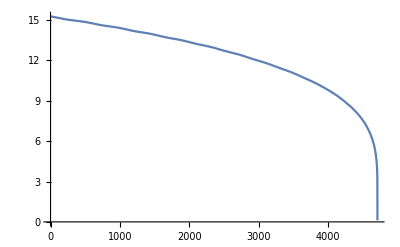

```mathematica
Plot[r[t],{t,0,tfinins}]
```

```mathematica
ScientificForm[r[tISCO]]
```

{4.83849}

```mathematica
Simplify[ 5/256(r[tISCO] M)^4/(m1 m2 M)]
```

{42.8182}

### We need the time derivative of r for the strain. For this to work we use an interpolating polynomial to model r and then differentiate it.

```mathematica
rtab=Table[r[t],{t,0,tfintab,dt}];
rvstime=Partition[Riffle[tArray,rtab],2];
rvstime1=MapAt[Delete[#,0]&,rvstime,{All,2}];
```

```mathematica
InterpolatingPolynomial[rvstime1,t];
```

General::munfl: (1.54626×10^-305)/1213. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.52522×10^-305)/-1168. is too small to represent as a normalized machine number; precision may be lost.

General::munfl: -(1.64744×10^-307)/128. is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Expand[%]
```

15.2703-0.000814712 t+0.0000256635 t^2-0.0000101749 t^3+1.98602×10^-6 t^4-2.3771×10^-7 t^5+1.91345×10^-8 t^6-1.10124×10^-9 t^7+4.73712×10^-11 t^8-1.57576×10^-12 t^9+4.16456×10^-14 t^10-8.94037×10^-16 t^11+1.5879×10^-17 t^12-2.36967×10^-19 t^13+3.01074×10^-21 t^14-3.29379×10^-23 t^15+3.13345×10^-25 t^16-2.61442×10^-27 t^17+1.92767×10^-29 t^18-1.26443×10^-31 t^19+7.42221×10^-34 t^20-3.91977×10^-36 t^21+1.87131×10^-38 t^22-8.1107×10^-41 t^23+3.204×10^-43 t^24-1.15768×10^-45 t^25+3.83837×10^-48 t^26-1.17126×10^-50 t^27+3.29828×10^-53 t^28-8.59269×10^-56 t^29+2.07576×10^-58 t^30-4.65961×10^-61 t^31+9.73869×10^-64 t^32-1.89853×10^-66 t^33+3.45805×10^-69 t^34-5.89412×10^-72 t^35+9.41484×10^-75 t^36-1.41123×10^-77 t^37+1.98755×10^-80 t^38-2.63318×10^-83 t^39+3.28516×10^-86 t^40-3.86353×10^-89 t^41+4.28718×10^-92 t^42-4.49258×10^-95 t^43+4.44946×10^-98 t^44-4.16803×10^-101 t^45+3.69544×10^-104 t^46-3.10305×10^-107 t^47+2.46918×10^-110 t^48-1.86291×10^-113 t^49+1.33326×10^-116 t^50-9.05552×10^-120 t^51+5.83928×10^-123 t^52-3.57606×10^-126 t^53+2.08057×10^-129 t^54-1.1503×10^-132 t^55+6.04481×10^-136 t^56-3.01981×10^-139 t^57+1.43437×10^-142 t^58-6.47848×10^-146 t^59+2.78252×10^-149 t^60-1.13649×10^-152 t^61+4.41407×10^-156 t^62-1.63017×10^-159 t^63+5.72393×10^-163 t^64-1.91053×10^-166 t^65+6.06071×10^-170 t^66-1.82679×10^-173 t^67+5.23016×10^-177 t^68-1.42182×10^-180 t^69+3.66856×10^-184 t^70-8.97963×10^-188 t^71+2.08399×10^-191 t^72-4.5829×10^-195 t^73+9.54314×10^-199 t^74-1.88025×10^-202 t^75+3.50218×10^-206 t^76-6.16093×10^-210 t^77+1.02254×10^-213 t^78-1.59929×10^-217 t^79+2.35408×10^-221 t^80-3.25637×10^-225 t^81+4.22634×10^-229 t^82-5.13728×10^-233 t^83+5.83676×10^-237 t^84-6.1845×10^-241 t^85+6.09588×10^-245 t^86-5.57356×10^-249 t^87+4.71187×10^-253 t^88-3.66961×10^-257 t^89+2.62166×10^-261 t^90-1.70978×10^-265 t^91+1.01211×10^-269 t^92-5.40144×10^-274 t^93+2.5779×10^-278 t^94-1.08949×10^-282 t^95+4.02785×10^-287 t^96-1.28251×10^-291 t^97+3.446×10^-296 t^98-7.59767×10^-301 t^99+1.3198×10^-305 t^100-1.69375×10^-310 t^101+1.42765×10^-315 t^102-5.93×10^-321 t^103

```mathematica
rinterp=Interpolation[rvstime1,InterpolationOrder->13]
```

InterpolatingFunction[…]

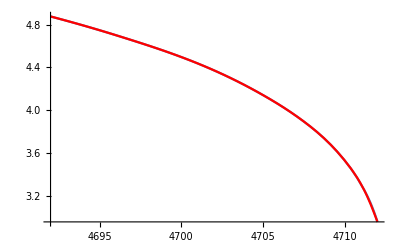

```mathematica
Show[Plot[r[t],{t,tfintab -TcIS,tfintab}],
Plot[rinterp[t],{t,tfintab - TcIS,tfintab},PlotStyle->Red]]
```

## Solving for the phase.

```mathematica
phid0PN[t_]:=((1-et3PN[t]^2)^(1/2))/(et3PN[t]*Cos[u3PNADMinterp[t]]-1)^2;
```

```mathematica
phid1PN[t_]:=-((et3PN[t](η-4)(et3PN[t]-Cos[u3PNADMinterp[t]]))/((1-et3PN[t]^2)^(1/2)(et3PN[t]*Cos[u3PNADMinterp[t]]-1)^3));
```

```mathematica
phid2PN[t_]:=(1/(12(1-et3PN[t]^2)^(3/2)(et3PN[t]*Cos[u3PNADMinterp[t]]-1)^5))((-12 η^2-18η)et3PN[t]^6+(20 η^2-26η-60)et3PN[t]^4+(-2 η^2+50η+75)et3PN[t]^2+((-14 η^2+8η-147)et3PN[t]^5+(8 η^2+22η+42)et3PN[t]^3)*Cos[u3PNADMinterp[t]]^3+((17 η^2-17η+48)et3PN[t]^6+(-4 η^2-38η+153)et3PN[t]^4+(5 η^2-35η+114)et3PN[t]^2)*Cos[u3PNADMinterp[t]]^2-36η+((-η^2+97η+12)et3PN[t]^5+(-16 η^2-74η-81)et3PN[t]^3+(-η^2+67η-246)et3PN[t])*Cos[u3PNADMinterp[t]]+(1-et3PN[t]^2)^(1/2)(et3PN[t]^3(36η-90)*Cos[u3PNADMinterp[t]]^3+((180-72η)et3PN[t]^4+(90-36η)et3PN[t]^2)*Cos[u3PNADMinterp[t]]^2+((144η-360)et3PN[t]^3+(90-36η)et3PN[t])*Cos[u3PNADMinterp[t]]+et3PN[t]^2(180-72η)+36η-90)+90);
```

```mathematica
phid3PN[t_]:=(1/(13440(1-et3PN[t]^2)^(5/2)(et3PN[t]*Cos[u3PNADMinterp[t]]-1)^7))((10080 η^3+40320 η^2-15120η)et3PN[t]^10+(-52640 η^3-13440 η^2+483280η)et3PN[t]^8+(84000 η^3-190400 η^2-17220 π^2 η-50048η-241920)et3PN[t]^6+(-52640 η^3+516880 η^2+68880 π^2 η-1916048η+262080)et3PN[t]^4+(4480 η^3-412160 η^2-30135 π^2 η+553008η+342720)et3PN[t]^2+((13440 η^3+94640 η^2-113680η-221760)et3PN[t]^9+(-11200 η^3-112000 η^2+12915 π^2 η+692928η-194880)et3PN[t]^7+(4480 η^3+8960 η^2-43050 π^2 η+1127280η-147840)et3PN[t]^5)*Cos[u3PNADMinterp[t]]^5+((-16240 η^3+12880 η^2+18480η)et3PN[t]^10+(16240 η^3-91840 η^2+17220 π^2 η-652192η+100800)et3PN[t]^8+(-55440 η^3+34160 η^2-30135 π^2 η-2185040η+2493120)et3PN[t]^6+(21840 η^3+86800 η^2+163590 π^2 η-5713888η+228480)et3PN[t]^4)Cos[u3PNADMinterp[t]]^4+((560 η^3-137200 η^2+388640η+241920)et3PN[t]^9+(30800 η^3-264880 η^2-68880 π^2 η+624128η+766080)et3PN[t]^7+(66640 η^3+612080 η^2-8610 π^2 η+6666080η-6652800)et3PN[t]^5+(-30800 η^3-294000 η^2-223860 π^2 η+9386432η)et3PN[t]^3)Cos[u3PNADMinterp[t]]^3+67200 η^2+((4480 η^3-20160 η^2+16800η)et3PN[t]^10+(3920 η^3+475440 η^2-17220 π^2 η+831952η-725760)et3PN[t]^8+(-75600 η^3+96880 η^2+154980 π^2 η-3249488η-685440)et3PN[t]^6+(5040 η^3-659120 η^2+25830 π^2 η-7356624η+6948480)et3PN[t]^4+(-5040 η^3+190960 η^2+137760 π^2 η-7307920η+107520)et3PN[t]^2)Cos[u3PNADMinterp[t]]^2-761600η+((-2240 η^3-168000 η^2-424480η)et3PN[t]^9+(28560 η^3+242480 η^2+34440 π^2 η-1340224η+725760)et3PN[t]^7+(-33040 η^3-754880 η^2-172200 π^2 η+5458480η-221760)et3PN[t]^5+(40880 η^3+738640 η^2+30135 π^2 η+1554048η-2936640)et3PN[t]^3+(-560 η^3-100240 η^2-43050 π^2 η+3284816η-389760)et3PN[t])Cos[u3PNADMinterp[t]]+(1-et3PN[t]^2)^(1/2)(((-127680 η^2+544320η-739200)et3PN[t]^7+(-53760 η^2-8610 π^2 η+674240η-67200)et3PN[t]^5)Cos[u3PNADMinterp[t]]^5+((161280 η^2-477120η+537600)et3PN[t]^8+(477120 η^2+17220 π^2 η-2894080η+2217600)et3PN[t]^6+(268800 η^2+25830 π^2 η-2721600η+1276800)et3PN[t]^4)Cos[u3PNADMinterp[t]]^4+((-524160 η^2+1122240η-940800)et3PN[t]^7+(-873600 η^2-68880 π^2 η+7705600η-3897600)et3PN[t]^5+(-416640 η^2-17220 π^2 η+3357760η-3225600)et3PN[t]^3)Cos[u3PNADMinterp[t]]^3+((604800 η^2-504000η-403200)et3PN[t]^6+(1034880 η^2+103320 π^2 η-11195520η+5779200)et3PN[t]^4+(174720 η^2-17220 π^2 η-486080η+2688000)et3PN[t]^2)Cos[u3PNADMinterp[t]]^2+((-282240 η^2-450240η+1478400)et3PN[t]^5+(-719040 η^2-68880 π^2 η+8128960η-5040000)et3PN[t]^3+(94080 η^2+25830 π^2 η-1585920η-470400)et3PN[t])Cos[u3PNADMinterp[t]]-67200 η^2+761600η+et3PN[t]^4(40320 η^2+309120η-672000)+et3PN[t]^2(208320 η^2+17220 π^2 η-2289280η+1680000)-8610 π^2 η-201600)+8610 π^2 η+201600)
```

```mathematica
phidot[t_]:=1/M(phid0PN[t]*x3PN[t]^(3/2)+phid1PN[t]*x3PN[t]^(5/2)+phid2PN[t]*x3PN[t]^(7/2)+phid3PN[t]*x3PN[t]^(9/2));
```

```mathematica
solphi3PN=NDSolve[{phiADM'[t]- phidot[t]==0,phiADM[0]==0},phiADM[t],{t,0,tfintab}, Method->{"StiffnessSwitching"},AccuracyGoal->Automatic, WorkingPrecision->$MinPrecision, PrecisionGoal->$MinPrecision];
```

NDSolve::precw: The precision of the differential equation ({{{-1. (Times[«3»]+Times[«6»]+Times[«5»]+Times[«5»])+phiADM'[t]}==0,phiADM[0]==0},{},{},{},{}}) is less than WorkingPrecision (20.).

```mathematica
phi[t_]:=Evaluate[phiADM[t]/.solphi3PN]
```

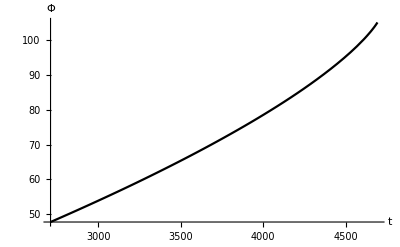

```mathematica
Plot[phi[t],{t,tfintab-100 TcIS,tfintab-TcIS},AxesLabel->{Style["t",Bold,16],Style["Φ",Bold,16]},PlotStyle->Black]
```

```mathematica
ScientificForm[phi[tISCO]]
```

{1.05227×10^2}

```mathematica
ScientificForm[phidot[tISCO]]
```

{7.5297×10^-2}

```mathematica
ScientificForm[phidot'[tISCO]]
```

{8.57723×10^-4}

## The Strain

```mathematica
hre[t_]:=-2M η((-rinterp'[t]^2+r[t]^2 phidot[t]^2+M r[t]^-1)Cos[2*phi[t]] +2*r[t]*rinterp'[t]*phidot[t]Sin[2*phi[t]]);
```

```mathematica
him[t_]:=-2M η((-rinterp'[t]^2+r[t]^2 phidot[t]^2+M r[t]^-1)Sin[2*phi[t]] -2*r[t]*rinterp'[t]*phidot[t]Cos[2*phi[t]]);
```

```mathematica
hins[t_]:=hre[t]-ⅈ*him[t];
```

Calculate Max and normalize strain

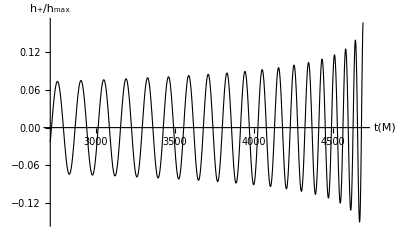

```mathematica
Plot[hre[t],{t,tfintab-100 TcIS,tfintab-TcIS},AxesLabel->{Style["t(M)",Bold,16],Style["h_+/h_max",Bold,16]},PlotStyle->{Thickness[0.002],Black}]
```

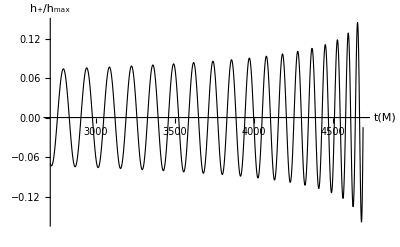

```mathematica
Plot[him[t],{t,tfintab-100 TcIS,tfintab-TcIS},AxesLabel->{Style["t(M)",Bold,16],Style["h_+/h_max",Bold,16]},PlotStyle->{Thickness[0.002],Black}]
```

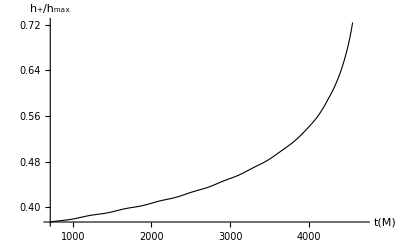

```mathematica
Plot[Abs[hins[t]]/Abs[hins[tfintab-TcIS]],{t,tfintab-200 TcIS,tfintab-TcIS},AxesLabel->{Style["t(M)",Bold,16],Style["h_+/h_max",Bold,16]},PlotStyle->{Thickness[0.002],Black}]
```

```mathematica
HampArray=Flatten[Table[Abs[hins[t]]/Abs[hins[tfintab-TcIS]],{t, tfintab-200TcIS,tfintab-TcIS,dt}]];
```

```mathematica
HamptArrayTcIS=Table[t,{t, tfintab-200 TcIS,tfintab-TcIS,dt}];
```

```mathematica
Hampvstime=Partition[Riffle[HamptArrayTcIS,HampArray],2];
```

```mathematica
(*Export["dropbox/dillon/paperplottingwork/e01hampdata.txt",Hampvstime]*)
```

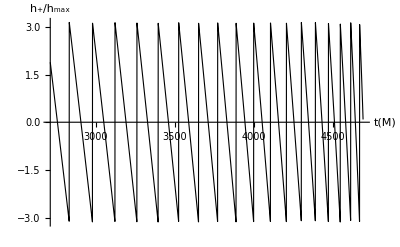

```mathematica
Plot[Arg[hins[t]],{t,tfintab-100 TcIS,tfintab-TcIS},AxesLabel->{Style["t(M)",Bold,16],Style["h_+/h_max",Bold,16]},PlotStyle->{Thickness[0.002],Black}]
```

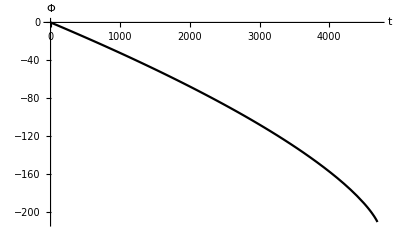

```mathematica
Plot[-2phi[t],{t,0,tfintab-TcIS},AxesLabel->{Style["t",Bold,16],Style["Φ",Bold,16]},PlotStyle->Black]
```

```mathematica
ArgArray=Flatten[Table[Arg[hins[t]],{t, 0,tfintab-TcIS,dt}]];
```

```mathematica
unwrapArgArray={{"[◼]", "PhaseUnwrap"}}[ArgArray];
```

```mathematica
tArrayTcIS=Table[t,{t,0,tfintab-TcIS,dt}];
```

```mathematica
Argunwrapvstime=Partition[Riffle[tArrayTcIS,-unwrapArgArray],2];
```

```mathematica
(*Export["dropbox/dillon/paperplottingwork/e01argunwrapdata.txt", Argunwrapvstime]*)
```

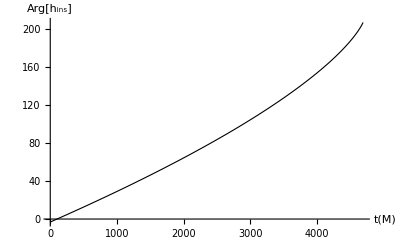

```mathematica
ListLinePlot[Argunwrapvstime,AxesLabel->{Style["t(M)",Bold,16],Style["Arg[h_ins]",Bold,16]},PlotStyle->{Thickness[0.002],Black}]
```